Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Below is the table used for calculating c-value for normal distribution.

```mathematica
(* α is level of significance; cvm is degrees of freedom; 100000 degrees==∞ *)
α={0.05,0.025,0.010,0.005,0.001}
cvm={{1,6.31,12.7, 31.8, 63.7, 318.3},{2,2.92, 4.30, 6.96, 9.92, 22.3},{3,2.35, 3.18, 4.54, 5.84, 10.2},{4,2.13, 2.78, 3.75, 4.60, 7.17},{5,2.02, 2.57, 3.36, 4.03, 5.89},{6,1.94, 2.45, 3.14, 3.71, 5.21},{7,1.89, 2.36, 3.00, 3.50, 4.79},{8,1.86, 2.31, 2.90, 3.36, 4.50},{9,1.83, 2.26, 2.82, 3.25, 4.30},{10,1.81, 2.23, 2.76, 3.17, 4.14},{11,1.80, 2.20, 2.72, 3.11, 4.02},{12,1.78, 2.18, 2.68, 3.05, 3.93},{13,1.77, 2.16, 2.65, 3.01, 3.85},{14,1.76, 2.14, 2.62, 2.98, 3.79},{15,1.75, 2.13, 2.60, 2.95, 3.73},{16,1.75, 2.12, 2.58, 2.92, 3.69},{17,1.74, 2.11, 2.57, 2.90, 3.65},{18,1.73, 2.10, 2.55, 2.88, 3.61},{19,1.73, 2.09, 2.54, 2.86, 3.58},{20,1.72, 2.09, 2.53, 2.85, 3.55},{22, 1.72, 2.07, 2.51, 2.82, 3.50},{24, 1.71, 2.06, 2.49, 2.80, 3.47},{26, 1.71, 2.06, 2.48, 2.78, 3.43},{28, 1.70, 2.05, 2.47, 2.76, 3.41},{30, 1.70, 2.04, 2.46, 2.75, 3.39},{40, 1.68, 2.02, 2.42, 2.70, 3.31},{50, 1.68, 2.01, 2.40, 2.68, 3.26},{100, 1.66, 1.98, 2.36, 2.63, 3.17},{200, 1.65, 1.97, 2.35, 2.60, 3.13},{100000, 1.65, 1.96, 2.33, 2.58, 3.09}};

critCVM=Interpolation[Flatten[Table[{{cvm[[i,1]],α[[j]]},cvm[[i,j+1]]},{j,5},{i,Length[cvm]}],1]]
```

{0.05,0.025,0.01,0.005,0.001}

InterpolatingFunction[{{1., 100000.}, {0.001, 0.05}}, <>]

Below is the table used for calculating c - value for chi-square distribution.

```mathematica
α={0.05,0.025,0.010,0.005}
cxm={{1,3.84, 5.02, 6.63, 7.88},{2,5.99, 7.38, 9.21, 10.60},{3,7.81, 9.35, 11.34, 12.84},{4,9.49, 11.14, 13.28, 14.86},{5,11.07, 12.83, 15.09, 16.75},{6,12.59, 14.45, 16.81, 18.55},{7,14.07, 16.01, 18.48, 20.28},{8,15.51, 17.53, 20.09, 21.95},{9,16.92, 19.02, 21.67, 23.59},{10,18.31, 20.48, 23.21, 25.19},{11,19.68, 21.92, 24.72, 26.76},{12,21.03, 23.34, 26.22, 28.30},{13,22.36, 24.74, 27.69, 29.82},{14,23.68, 26.12, 29.14, 31.32},{15,25.00, 27.49, 30.58, 32.80},{16,26.30, 28.85, 32.00, 34.27},{17,27.59, 30.19, 33.41, 35.72},{18,28.87, 31.53, 34.81, 37.16},{19,30.14, 32.85, 36.19, 38.58},{20,31.41, 34.17, 37.57, 40.00},{21, 32.7, 35.5, 38.9, 41.4},{22, 33.9, 36.8, 40.3, 42.8},{23, 35.2, 38.1, 41.6, 44.2},{24, 36.4, 39.4, 43.0, 45.6},{25, 37.7, 40.6, 44.3, 46.9},{26, 38.9, 41.9, 45.6, 48.3},{27, 40.1, 43.2, 47.0, 49.6},{28, 41.3, 44.5, 48.3, 51.0},{29, 42.6, 45.7, 49.6, 52.3},{30, 43.8, 47.0, 50.9, 53.7}, {40, 55.8, 59.3, 63.7, 66.8},{50, 67.5, 71.4, 76.2, 79.5},{60, 79.1, 83.3, 88.4, 92.0},{70, 90.5, 95.0, 100.4, 104.2},{80, 101.9, 106.6, 112.3, 116.3},{90, 113.1, 118.1, 124.1, 128.3},{100, 124.3, 129.6, 135.8, 140.2},{200,1/2(√(199-1)+1.64)^2,1/2(√(199-1)+1.96)^2,1/2(√(199-1)+2.33)^2,1/2(√(199-1)+2.58)^2}};
(*in case degrees of freedom goes above 199, the applicable number can be substituted in to replace 199 above in the last line, with the understanding that the values in the last line are approximate.*)

critCXM=Interpolation[Flatten[Table[{{cxm[[i,1]],α[[j]]},cxm[[i,j+1]]},{j,4},{i,Length[cxm]}],1]]
```

{0.05,0.025,0.01,0.005}

InterpolatingFunction[{{1., 200.}, {0.005, 0.05}}, <>]

3.  Are oil filters of type A better than type B filters if in 11 trials, A gave cleaner oil than B in 7 cases, B gave cleaner oil than A in 1 case, whereas in 3 of the trials the results for A and B were practically the same?

My first inclination is to try the χ^2 test. The three cases where A and B acted the same are dropped. I have 8 trials, and the hypothesis is that they are equal. Thus the outcomes should be 4 and 4.

```mathematica
N[(7-4)^2/4+(1-4)^2/4]
```

4.5

```mathematica
critCXM[1,0.05]
```

3.84

The result is the expected one, that the hypothesis of equal outcomes is false, and that A is better. But the sample size does not justify using the χ^2 test. So I need to look again.

```mathematica
NProbability[6<x,x\[Distributed]BinomialDistribution[8,1/2]]
```

0.0351563

The answer in the green cell above matches that of the text.

I don’t know if that is exactly right though.

```mathematica
NProbability[x==7,x\[Distributed]BinomialDistribution[8,1/2]]
```

0.03125

The above yellow cell fits the circumstances better, though it does not match the text answer.

4. Does a process of producing stainless steel pipes of length 20 ft for nuclear reactors need adjustment if, in a sample, 4 pipes have the exact length and 15 are shorter and 3 longer than 20 ft? Use the normal approximation of the binomial distribution.

5. Do the computations in problem 4 without the use of the DeMoivre-Laplace limit theorem in section 24.8.

As in previous problems, I discard the cases that do not contribute to a decision. I’m only interested in the 15 short and the 3 long. I assume that in cutting the pipes, an equal probability should be assigned to the chance of cutting long and short. The division into 15 short and 3 long seems oddly unbalanced. I look at the probability

```mathematica
NProbability[x<4,x\[Distributed]BinomialDistribution[18,1/2]]
```

0.00376892

```mathematica
(0.5)^18(1+18+153+816)
```

0.00376892

The answer in the green cell matches the answer in the text, which is provided above, in factored form.

6. Thirty new employees were grouped into 15 pairs of similar intelligence and experience and were then instructed in data processing by an old method (A) applied to one (randomly selected) person of each pair, and by a new presumably better method (B) applied to the other person of each pair. Test for equality of methods against the alternative that (B) is better than (A), using the following scores obtained after the end of the training period.

A | 60 | 70 | 80 | 85 | 75 | 40 | 70 | 45 | 95 | 80 | 90 | 60 | 80 | 75 | 65
B | 65 | 85 | 85 | 80 | 95 | 65 | 100 | 60 | 90 | 85 | 100 | 75 | 90 | 60 | 80

7. Assuming normality, solve problem 6 by a suitable test from section 25.4.

The Mathematica docs have an example very similar in the PairedTTest section.

```mathematica
sA={60, 70, 80, 85, 75, 40, 70, 45, 95, 80, 90, 60, 80, 75, 65}
```

{60,70,80,85,75,40,70,45,95,80,90,60,80,75,65}

```mathematica
sB={65, 85, 85, 80, 95, 65, 100, 60, 90, 85, 100, 75, 90, 60, 80}
```

{65,85,85,80,95,65,100,60,90,85,100,75,90,60,80}

In the documentary example, two different tests are compared, the ACT and the SAT, and thus need to be normalized. I try that route too out of curiosity.

```mathematica
ssA=N[(sA-Mean[sA])/StandardDeviation[sA]];
```

```mathematica
ssB=N[(sB-Mean[sB])/StandardDeviation[sB]];
```

Displaying histograms of normalized (top) and raw (bottom) sample sets.

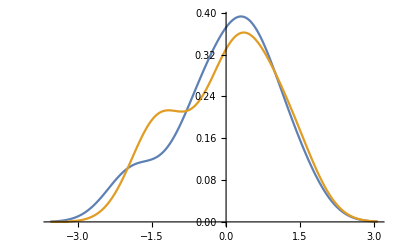
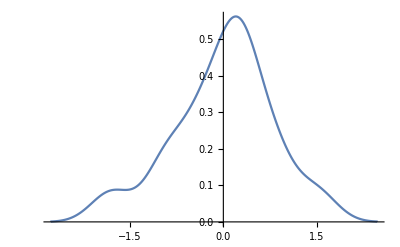

```mathematica
Row[{SmoothHistogram[{ssA,ssB}],SmoothHistogram[ssB-ssA]}]
```

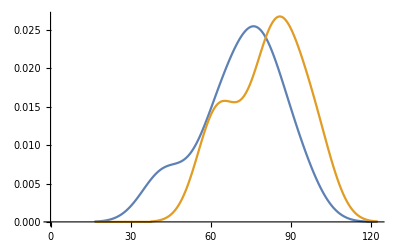
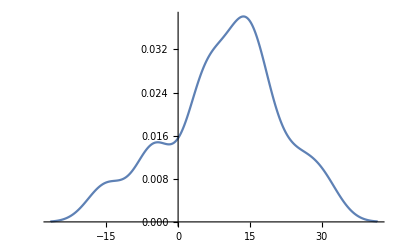

```mathematica
Row[{SmoothHistogram[{sA,sB}],SmoothHistogram[sB-sA]}]
```

Displaying the paired t-test comparison of the normalized sets. It does not make a forceful case.

```mathematica
PairedTTest[{ssA,ssB},0,"TestDataTable",AlternativeHypothesis->"Greater"]
```

| Statistic | P-Value
Paired T | -8.82471×10^-17 | 0.5

Displaying the paired t-test of the raw sets. Under the assumption that the same or equivalent tests were used for both testing sessions, the p-value in the raw comparison is fairly persuasive.

```mathematica
PairedTTest[{sA,sB},0,"TestDataTable",AlternativeHypothesis->"Greater"]
```

| Statistic | P-Value
Paired T | -3.15345 | 0.996478

8. In a clinical experiment, each of 10 patients were given two different sedatives A and B. The following table shows the effect (increase of sleeping time, measured in hours). Using the sign test, find out whether the difference is significant.

A | 1.9 | 0.8 | 1.1 | 0.1 | -0.1 | 4.4 | 5.5 | 1.6 | 4.6 | 3.4
B | 0.7 | -1.6 | -0.2 | -1.2 | -0.1 | 3.4 | 3.7 | 0.8 | 0.0 | 2.0
Difference | 1.2 | 2.4 | 1.3 | 1.3 | 0.0 | 1.0 | 1.8 | 0.8 | 4.6 | 1.4

9. Assuming that the populations corresponding to the samples of problem 8 are normal, apply a suitable test for the normal distribution.

Just from scanning the two sets, sed1 seems definitely the more effective, and the p-value below endorses that interpretation.

```mathematica
sed1={1.9, 0.8, 1.1, 0.1, -0.1, 4.4, 5.5, 1.6, 4.6, 3.4}
```

{1.9,0.8,1.1,0.1,-0.1,4.4,5.5,1.6,4.6,3.4}

```mathematica
sed2={0.7, -1.6, -0.2, -1.2, -0.1, 3.4, 3.7, 0.8, 0.0, 2.0}
```

{0.7,-1.6,-0.2,-1.2,-0.1,3.4,3.7,0.8,0.,2.}

```mathematica
PairedTTest[{sed2,sed1},0,"TestDataTable",AlternativeHypothesis->"Greater"]
```

| Statistic | P-Value
Paired T | -4.06213 | 0.998584

11. How would you proceed in the sign test if the hypothesis is μ̃ = OverTilde[μ_0] (any number) instead of μ̃ = 0?

In the Mathematica version of SignTest, the input for μ̃ is not restricted.

13. Does the amount of fertilizer increase the yield of wheat X [kg/plot]? Use a sample of values ordered according to increasing amounts of fertilizer:
33.4, 35.3, 31.6, 35.0, 36.1, 37.6, 36.5, 38.7

```mathematica
wheat={33.4, 35.3, 31.6, 35.0, 36.1, 37.6, 36.5, 38.7}
```

{33.4,35.3,31.6,35.,36.1,37.6,36.5,38.7}

```mathematica
d2=Range[8];
```

```mathematica
duo2=Table[{d2[[n]],wheat[[n]]},{n,1,8}];
```

```mathematica
p2=ListLinePlot[duo2,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Red,PlotRange->{{0,9},{30,40}}];
```

```mathematica
Fit[duo2,{1,x},x]
```

32.1929+0.740476 x

Curve fitting shows an unmistakable increasing trend. Though it’s easy for me to toss out a Fit command, it is worth remembering that Mathematica does a lot of least squares work to come up with it. And numerically, the sign of the coefficient of x reassures me that it is increasing.

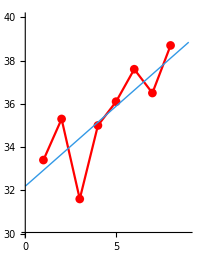

```mathematica
p3=ListLinePlot[duo2,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Red,PlotRange->{{0,9},{30,40}},Epilog->{{RGBColor[0.2,0.6,0.9],Line[{{0,32.19},{9,32.19+0.74*9}}]}}]
```

15. Does an increase in temperature cause an increase of the yield of a chemical reaction from which the following sample was taken?

Temperature[degC] | 10 | 20 | 30 | 40 | 60 | 80
Yield[kg/min] | 0.6 | 1.1 | 0.9 | 1.6 | 1.2 | 2.0

```mathematica
chem={0.6, 1.1, 0.9, 1.6, 1.2, 2.0}
```

{0.6,1.1,0.9,1.6,1.2,2.}

```mathematica
d3=Range[10,80,10]
```

```mathematica
dchem=Table[{d3[[n]],chem[[n]]},{n,1,6}];
```

```mathematica
pch=ListLinePlot[dchem,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Red,PlotRange->{{0,70},{0,2.5}}];
```

```mathematica
Fit[dchem,{1,x},x]
```

0.433333+0.0228571 x

Again the increasing trend is clear, especially at the shown aspect ratio and plot range. The small but positive x-coefficient objectively affirms the increasing tendency.

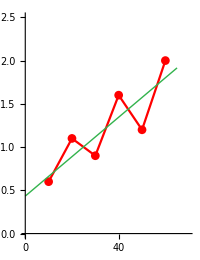

```mathematica
pch2=ListLinePlot[dchem,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Red,PlotRange->{{0,70},{0,2.5}},Epilog->{{RGBColor[0.2,0.7,0.3],Line[{{0,.4333},{65,.4333+0.0228*65}}]}}]
```